Část na parametry

```mathematica
h = 1
V =10
```

1

10

```mathematica
x1 = -5
```

-5

```mathematica
x2=0
```

0

Část na výpočet βstart, βend a čas

```mathematica
X2 =  h(-Sec[B]+Sec[β])
```

-Sec[B]+Sec[β]

```mathematica
X1 = 1/2 h(-ArcTanh[Sin[B]]+ArcTanh[Sin[β]]-Sec[B] Tan[B]+2 Sec[B] Tan[β]-Sec[β] Tan[β])
```

1/2 (-ArcTanh[Sin[B]]+ArcTanh[Sin[β]]-Sec[B] Tan[B]+2 Sec[B] Tan[β]-Sec[β] Tan[β])

```mathematica
res = FindRoot[{X1==x1,X2==x2},{{β,0},{B,1}},PrecisionGoal->Infinity]
```

{β→-1.06041,B→1.06041}

```mathematica
βend = B /.res
```

1.06041

```mathematica
βstart = β /. res
```

-1.06041

```mathematica
t1 = -(h/V)(Tan[βstart]-Tan[βend])
```

0.35723

Kontrolní část

```mathematica
h(1/(Cos[βstart])-1/(Cos[βend]))
```

8.88178×10^-16

```mathematica
1/2 h(-ArcTanh[Sin[βend]]+ArcTanh[Sin[βstart]]-Sec[βend] Tan[βend]+2 Sec[βend] Tan[βstart]-Sec[βstart] Tan[βstart])
```

-5.

```mathematica
rce = {x'[t]==V*Cos[β[t]]-(V/h)y[t],y'[t]==V*Sin[β[t]],β'[t]==(V/h)(Cos[β[t]])^2}
```

{x'[t]==10 Cos[β[t]]-10 y[t],y'[t]==10 Sin[β[t]],β'[t]==10 Cos[β[t]]^2}

```mathematica
sol1 = NDSolve[Join[rce,{x[0]==x1,y[0]==x2,β[0]==βstart}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

```mathematica
{x[t],y[t]}/.sol1
```

{{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}}

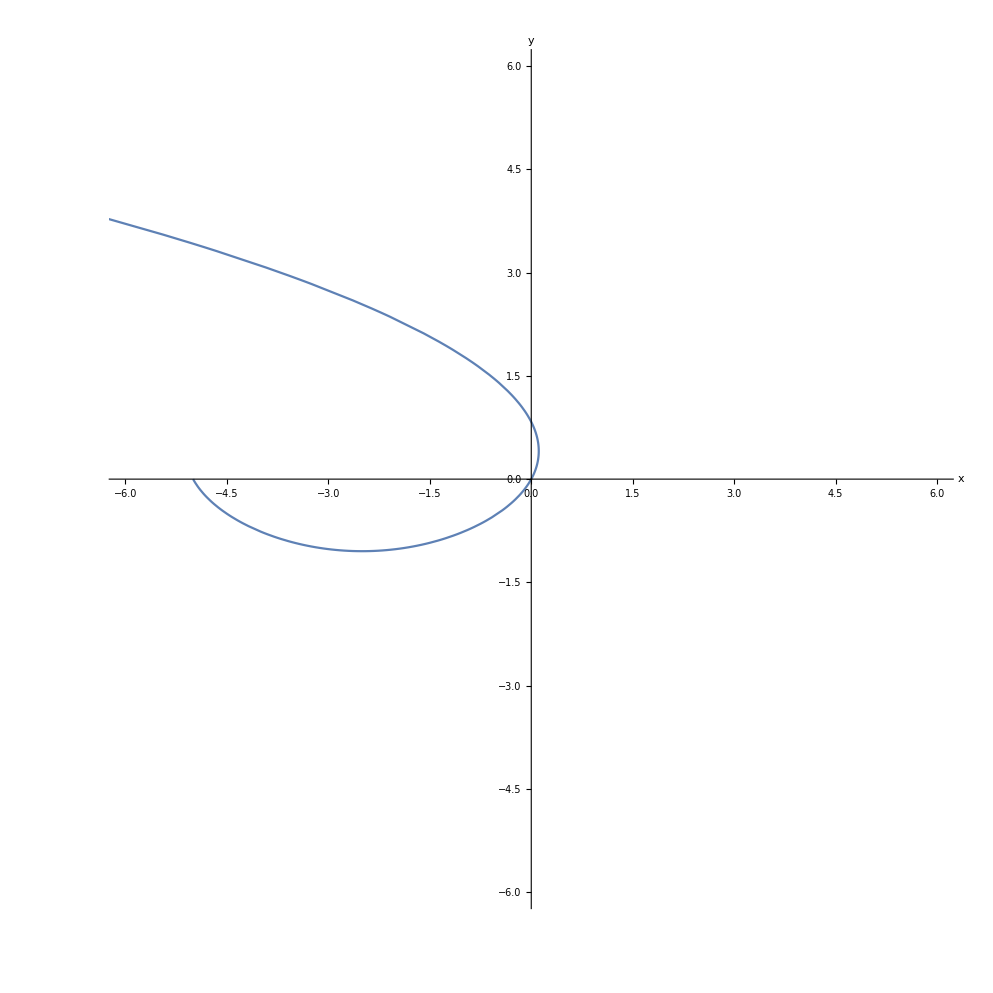

```mathematica
ParametricPlot[Table[{x[t],y[t]}/.sol1],{t,0,10},AxesLabel->{x,y},PlotRange->{{-6,6},{-6,6}}]
```